# Classifying Stocks by Their Return “Fingerprints”

By Aaliyah Sayed

In the stock market, the returns (%  change in price of the stock between days) of any particular stock create a fingerprint unique to that stock. For example, the returns of Tesla and Johnson &  Johnson are very different, since they are shaped by variable factors such as industry, size, and volatility. In this project, I used machine learning  to analyze the “return fingerprint” of stocks in the S&P 500. Would the computer tell me that Facebook and Twitter are similar, if I gave it no context? To isolate the return fingerprint from the rest of the variable factors, I trained the computer on pure Date List Plots.  I could analyze the impact of the variable factors, how people can use what they know about particular stocks to get a better overview of the market, and the accuracy and precision of computer results.  I aimed to correctly group stocks by fingerprint (within the time frame of a year), and analyze the correlation within the subgroups.

## Importing Data

The Wolfram databases store a wide range of financial data, so I was able to import all of my data directly and without parsing. I imported the returns of all stocks in the S&P 500 and created a list of DateListPlots to store the graphs. I removed the axes, but the range of all of the plots is { -10,10}.

The first line creates an association map of the imported data, and the second line uses the data and creates a list of date list plots.

```mathematica
moreReturns=AssociationMap[FinancialData[#,"Return","Jan. 1 2019"]&,EntityList[ EntityClass["Financial","SP500"]]];
```

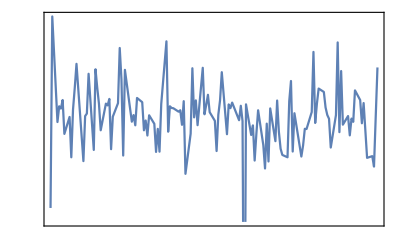
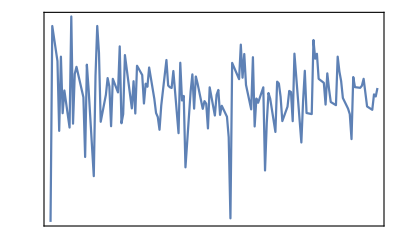
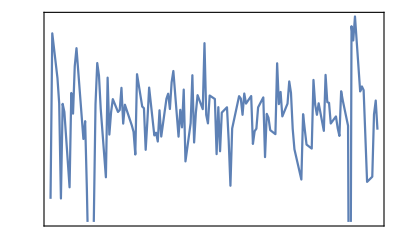
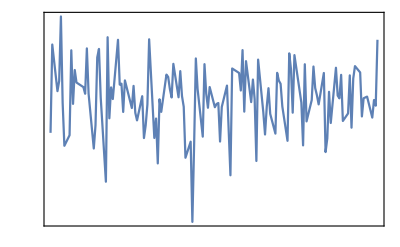
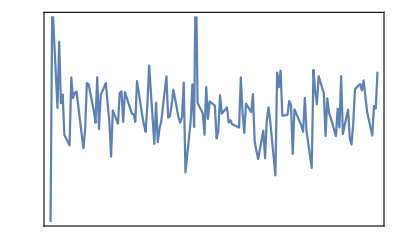
<|3M→-Graphics-,Abbott Laboratories→-Graphics-,AbbVie→-Graphics-,Abiomed→-Graphics-,Accenture→-Graphics-|>

```mathematica
stockReturnsPlot=DateListPlot[#,FrameTicks -> None]&  /@DeleteMissing[moreReturns];
Take[stockReturnsPlot,5]
```

## Initial Feature Space Plot

With all of the DateListPlots formatted correctly, I FeatureSpacePlotted the results. I discovered some patterns when hovering over datapoints (Adobe and Microsoft are near each other), but there are not enough features to visualize or comprehend the results.

```mathematica
FeatureSpacePlot[stockReturnsPlot]
```

-Graphics-

## Grouping By Sector

The next step was to obtain a list of industries and bucket the stocks by their industry.

These two lines create a list of the industries in the S&P 500. The third line buckets the stocks.

```mathematica
snpSectorsAll=AssociationMap[EntityValue[#,"Sector"]&,Keys[moreReturns]];
```

```mathematica
plotSectors=Values[snpSectorsAll]//Union
```

{Advertising And Marketing Services,Aerospace And Defense,Airlines,Application Software,Autos,Banks,Beverages Alcoholic,Brokers And Exchanges,Building Materials,Business Services,Chemicals,Communication Equipment,Communication Services,Computer Hardware,Consulting And Outsourcing,Consumer Packaged Goods,Credit Services,Drug Manufacturers,Engineering And Construction,Entertainment,Health Care Providers,Homebuilding And Construction,Industrial Distribution,Industrial Products,Insurance,Insurance Specialty,Manufacturing Apparel And Furniture,Medical Diagnostics And Research,Medical Distribution,Metals And Mining,Personal Services,Real Estate Services,REI Ts,Restaurants,Retail Apparel And Specialty,Retail Defensive,Semiconductors,Tobacco Products,Transportation And Logistics,Travel And Leisure,Truck Manufacturing,Utilities Regulated,Missing[NotAvailable]}

```mathematica
stockSectorsAll=GroupBy[Normal[snpSectorsAll],Last->First];
Take[stockSectorsAll,1]
```

<|Industrial Products→{3M,Ametek,A.O. Smith,Avery Dennison,Cummins,Dover,Eaton,Emerson,Flowserve,General Electric,Honeywell,Illinois Tool Works,Ingersoll-Rand,Parker Hannifin,Pentair,Rockwell Automation,Roper Industries,Snap-On,Stanley Black & Decker,Xylem}|>

## Mapping Sectors to Colors

I created a color table of 43 colors:

```mathematica
colorTable=Table[Hue[n/50],{n,1,43}]
```

{Hue[Rational[1, 50]],Hue[Rational[1, 25]],Hue[Rational[3, 50]],Hue[Rational[2, 25]],Hue[Rational[1, 10]],Hue[Rational[3, 25]],Hue[Rational[7, 50]],Hue[Rational[4, 25]],Hue[Rational[9, 50]],Hue[Rational[1, 5]],Hue[Rational[11, 50]],Hue[Rational[6, 25]],Hue[Rational[13, 50]],Hue[Rational[7, 25]],Hue[Rational[3, 10]],Hue[Rational[8, 25]],Hue[Rational[17, 50]],Hue[Rational[9, 25]],Hue[Rational[19, 50]],Hue[Rational[2, 5]],Hue[Rational[21, 50]],Hue[Rational[11, 25]],Hue[Rational[23, 50]],Hue[Rational[12, 25]],Hue[Rational[1, 2]],Hue[Rational[13, 25]],Hue[Rational[27, 50]],Hue[Rational[14, 25]],Hue[Rational[29, 50]],Hue[Rational[3, 5]],Hue[Rational[31, 50]],Hue[Rational[16, 25]],Hue[Rational[33, 50]],Hue[Rational[17, 25]],Hue[Rational[7, 10]],Hue[Rational[18, 25]],Hue[Rational[37, 50]],Hue[Rational[19, 25]],Hue[Rational[39, 50]],Hue[Rational[4, 5]],Hue[Rational[41, 50]],Hue[Rational[21, 25]],Hue[Rational[43, 50]]}

And I created an association thread to map all of the industries to different colors:

```mathematica
sectorsMapped=AssociationThread[Keys[stockSectorsAll]-> colorTable]
```

<|Industrial Products→Hue[Rational[1, 50]],Missing[NotAvailable]→Hue[Rational[1, 25]],Drug Manufacturers→Hue[Rational[3, 50]],Application Software→Hue[Rational[2, 25]],Retail Apparel And Specialty→Hue[Rational[1, 10]],Semiconductors→Hue[Rational[3, 25]],Utilities Regulated→Hue[Rational[7, 50]],Medical Diagnostics And Research→Hue[Rational[4, 25]],REI Ts→Hue[Rational[9, 50]],Chemicals→Hue[Rational[1, 5]],Airlines→Hue[Rational[11, 50]],Consulting And Outsourcing→Hue[Rational[6, 25]],Credit Services→Hue[Rational[13, 50]],Tobacco Products→Hue[Rational[7, 25]],Insurance→Hue[Rational[3, 10]],Communication Services→Hue[Rational[8, 25]],Medical Distribution→Hue[Rational[17, 50]],Computer Hardware→Hue[Rational[9, 25]],Brokers And Exchanges→Hue[Rational[19, 50]],Autos→Hue[Rational[2, 5]],Consumer Packaged Goods→Hue[Rational[21, 50]],Metals And Mining→Hue[Rational[11, 25]],Business Services→Hue[Rational[23, 50]],Banks→Hue[Rational[12, 25]],Aerospace And Defense→Hue[Rational[1, 2]],Travel And Leisure→Hue[Rational[13, 25]],Beverages Alcoholic→Hue[Rational[27, 50]],Manufacturing Apparel And Furniture→Hue[Rational[14, 25]],Real Estate Services→Hue[Rational[29, 50]],Entertainment→Hue[Rational[3, 5]],Restaurants→Hue[Rational[31, 50]],Transportation And Logistics→Hue[Rational[16, 25]],Communication Equipment→Hue[Rational[33, 50]],Retail Defensive→Hue[Rational[17, 25]],Health Care Providers→Hue[Rational[7, 10]],Homebuilding And Construction→Hue[Rational[18, 25]],Insurance Specialty→Hue[Rational[37, 50]],Industrial Distribution→Hue[Rational[19, 25]],Engineering And Construction→Hue[Rational[39, 50]],Personal Services→Hue[Rational[4, 5]],Advertising And Marketing Services→Hue[Rational[41, 50]],Building Materials→Hue[Rational[21, 25]],Truck Manufacturing→Hue[Rational[43, 50]]|>

## Initial Prototype

This code creates a dummy manipulate to simulate the user interface of my project.

```mathematica
sample=Manipulate[FeatureSpacePlot[stockReturnsPlot],{sectors,plotSectors,ControlType->TogglerBar,Appearance-> "Row"}]
```

## Mapping Colors

Once I had the stocks mapped to the sectors and the sectors mapped to the colors, I wrote a function to map the stocks to the colors.

This function takes a particular stock as a parameter, and it called on sectorsMapped and snpSectorsAll to return the corresponding colors.

```mathematica
stockColorFunction[a_]:= sectorsMapped[snpSectorsAll[a]]
```

This line gives me a list of the color values for each stock, without the stock names.

```mathematica
stockColorFunction/@Keys[moreReturns]
```

{Hue[Rational[1, 50]],Hue[Rational[1, 25]],Hue[Rational[3, 50]],Hue[Rational[1, 25]],Hue[Rational[2, 25]],Hue[Rational[2, 25]],Hue[Rational[1, 10]],Hue[Rational[3, 25]],Hue[Rational[2, 25]],Hue[Rational[7, 50]],Hue[Rational[1, 25]],Hue[Rational[1, 25]],Hue[Rational[4, 25]],Hue[Rational[9, 50]],Hue[Rational[1, 5]],Hue[Rational[2, 25]],Hue[Rational[1, 5]],Hue[Rational[11, 50]],Hue[Rational[9, 50]],Hue[Rational[1, 25]],Hue[Rational[1, 25]],Hue[Rational[6, 25]],Hue[Rational[3, 50]],Hue[Rational[13, 50]],Hue[Rational[7, 50]],Hue[Rational[1, 25]],Hue[Rational[1, 25]],Hue[Rational[1, 25]],Hue[Rational[7, 25]],Hue[Rational[1, 10]],Hue[Rational[7, 50]],Hue[Rational[11, 50]],Hue[Rational[7, 50]],Hue[Rational[13, 50]],Hue[Rational[3, 10]],Hue[Rational[8, 25]],Hue[Rational[7, 50]],Hue[Rational[1, 25]],Hue[Rational[17, 50]],Hue[Rational[1, 50]],Hue[Rational[3, 50]],Hue[Rational[9, 25]],Hue[Rational[1, 25]],Hue[Rational[3, 25]],Hue[Rational[2, 25]],Hue[Rational[1, 25]],Hue[Rational[19, 50]],Hue[Rational[1, 50]],Hue[Rational[1, 25]],Hue[Rational[9, 25]],Hue[Rational[3, 25]],Hue[Rational[2, 5]],Hue[Rational[21, 50]],Hue[Rational[11, 25]],Hue[Rational[9, 25]],Hue[Rational[19, 50]],Hue[Rational[3, 10]],Hue[Rational[8, 25]],Hue[Rational[7, 50]],Hue[Rational[2, 25]],Hue[Rational[23, 50]],Hue[Rational[1, 10]],Hue[Rational[9, 50]],Hue[Rational[1, 50]],Hue[Rational[1, 25]],Hue[Rational[1, 25]],Hue[Rational[12, 25]],Hue[Rational[1, 25]],Hue[Rational[12, 25]],Hue[Rational[1, 25]],Hue[Rational[1, 25]],Hue[Rational[3, 10]],Hue[Rational[1, 10]],Hue[Rational[3, 50]],Hue[Rational[1, 25]],Hue[Rational[1, 25]],Hue[Rational[1, 2]],Hue[Rational[2, 5]],Hue[Rational[9, 50]],Hue[Rational[1, 25]],Hue[Rational[13, 25]],Hue[Rational[3, 50]],Hue[Rational[3, 25]],Hue[Rational[23, 50]],Hue[Rational[27, 50]],Hue[Rational[1, 25]],Hue[Rational[2, 25]],Hue[Rational[21, 50]],Hue[Rational[13, 50]],Hue[Rational[14, 25]],Hue[Rational[17, 50]],Hue[Rational[2, 5]],Hue[Rational[13, 25]],Hue[Rational[1, 25]],Hue[Rational[19, 50]],Hue[Rational[29, 50]],Hue[Rational[3, 5]],Hue[Rational[1, 5]],Hue[Rational[3, 50]],Hue[Rational[1, 25]],Hue[Rational[7, 50]],Hue[Rational[8, 25]],Hue[Rational[2, 25]],Hue[Rational[1, 25]],Hue[Rational[19, 50]],Hue[Rational[8, 25]],Hue[Rational[1, 25]],Hue[Rational[31, 50]],Hue[Rational[16, 25]],Hue[Rational[1, 25]],Hue[Rational[21, 50]],Hue[Rational[1, 25]],Hue[Rational[1, 25]],Hue[Rational[1, 25]],Hue[Rational[23, 50]],Hue[Rational[33, 50]],Hue[Rational[12, 25]],Hue[Rational[2, 25]],Hue[Rational[12, 25]],Hue[Rational[21, 50]],Hue[Rational[19, 50]],Hue[Rational[7, 50]],Hue[Rational[1, 25]],Hue[Rational[2, 25]],Hue[Rational[21, 50]],Hue[Rational[8, 25]],Hue[Rational[12, 25]],Hue[Rational[21, 50]],Hue[Rational[1, 25]],Hue[Rational[1, 25]],Hue[Rational[7, 50]],Hue[Rational[27, 50]],Hue[Rational[1, 25]],Hue[Rational[2, 5]],Hue[Rational[9, 25]],Hue[Rational[21, 50]],Hue[Rational[17, 25]],Hue[Rational[9, 50]],Hue[Rational[16, 25]],Hue[Rational[1, 50]],Hue[Rational[1, 25]],Hue[Rational[4, 25]],Hue[Rational[31, 50]],Hue[Rational[7, 10]],Hue[Rational[7, 50]],Hue[Rational[11, 50]],Hue[Rational[1, 25]],Hue[Rational[1, 25]],Hue[Rational[1, 25]],Hue[Rational[9, 50]],Hue[Rational[13, 50]],Hue[Rational[3, 5]],Hue[Rational[3, 5]],Hue[Rational[8, 25]],Hue[Rational[3, 5]],Hue[Rational[17, 25]],Hue[Rational[17, 25]],Hue[Rational[7, 50]],Hue[Rational[1, 50]],Hue[Rational[1, 5]],Hue[Rational[18, 25]],Hue[Rational[7, 50]],Hue[Rational[7, 50]],Hue[Rational[9, 50]],Hue[Rational[1, 25]],Hue[Rational[2, 25]],Hue[Rational[1, 5]],Hue[Rational[1, 50]],Hue[Rational[1, 10]],Hue[Rational[1, 5]],Hue[Rational[7, 50]],Hue[Rational[1, 25]],Hue[Rational[2, 25]],Hue[Rational[3, 50]],Hue[Rational[1, 50]],Hue[Rational[7, 50]],Hue[Rational[1, 25]],Hue[Rational[23, 50]],Hue[Rational[9, 50]],Hue[Rational[9, 50]],Hue[Rational[21, 50]],Hue[Rational[19, 50]],Hue[Rational[37, 50]],Hue[Rational[7, 50]],Hue[Rational[7, 50]],Hue[Rational[7, 50]],Hue[Rational[13, 25]],Hue[Rational[16, 25]],Hue[Rational[9, 50]],Hue[Rational[9, 50]],Hue[Rational[1, 25]],Hue[Rational[2, 25]],Hue[Rational[1, 25]],Hue[Rational[19, 25]],Hue[Rational[9, 50]],Hue[Rational[16, 25]],Hue[Rational[23, 50]],Hue[Rational[12, 25]],Hue[Rational[7, 50]],Hue[Rational[12, 25]],Hue[Rational[23, 50]],Hue[Rational[23, 50]],Hue[Rational[9, 25]],Hue[Rational[1, 50]],Hue[Rational[39, 50]],Hue[Rational[1, 25]],Hue[Rational[1, 25]],Hue[Rational[2, 5]],Hue[Rational[2, 25]],Hue[Rational[9, 25]],Hue[Rational[14, 25]],Hue[Rational[14, 25]],Hue[Rational[3, 5]],Hue[Rational[3, 5]],Hue[Rational[1, 25]],Hue[Rational[11, 25]],Hue[Rational[1, 10]],Hue[Rational[9, 25]],Hue[Rational[2, 25]],Hue[Rational[1, 2]],Hue[Rational[1, 50]],Hue[Rational[21, 50]],Hue[Rational[2, 5]],Hue[Rational[1, 10]],Hue[Rational[3, 50]],Hue[Rational[23, 50]],Hue[Rational[19, 50]],Hue[Rational[1, 25]],Hue[Rational[14, 25]],Hue[Rational[2, 5]],Hue[Rational[33, 50]],Hue[Rational[13, 25]],Hue[Rational[7, 10]],Hue[Rational[9, 50]],Hue[Rational[1, 25]],Hue[Rational[17, 50]],Hue[Rational[21, 50]],Hue[Rational[1, 25]],Hue[Rational[9, 25]],Hue[Rational[33, 50]],Hue[Rational[13, 25]],Hue[Rational[1, 25]],Hue[Rational[1, 25]],Hue[Rational[1, 10]],Hue[Rational[1, 50]],Hue[Rational[21, 50]],Hue[Rational[9, 50]],Hue[Rational[4, 5]],Hue[Rational[1, 25]],Hue[Rational[12, 25]],Hue[Rational[1, 2]],Hue[Rational[2, 25]],Hue[Rational[4, 25]],Hue[Rational[23, 50]],Hue[Rational[1, 50]],Hue[Rational[4, 25]],Hue[Rational[1, 25]],Hue[Rational[1, 50]],Hue[Rational[3, 25]],Hue[Rational[19, 50]],Hue[Rational[1, 5]],Hue[Rational[1, 25]],Hue[Rational[41, 50]],Hue[Rational[2, 25]],Hue[Rational[1, 25]],Hue[Rational[4, 25]],Hue[Rational[1, 25]],Hue[Rational[3, 25]],Hue[Rational[9, 50]],Hue[Rational[23, 50]],Hue[Rational[39, 50]],Hue[Rational[16, 25]],Hue[Rational[1, 25]],Hue[Rational[21, 50]],Hue[Rational[39, 50]],Hue[Rational[3, 50]],Hue[Rational[12, 25]],Hue[Rational[33, 50]],Hue[Rational[16, 25]],Hue[Rational[21, 50]],Hue[Rational[12, 25]],Hue[Rational[9, 25]],Hue[Rational[21, 50]],Hue[Rational[9, 50]],Hue[Rational[1, 25]],Hue[Rational[3, 25]],Hue[Rational[1, 10]],Hue[Rational[21, 50]],Hue[Rational[17, 25]],Hue[Rational[1, 10]],Hue[Rational[1, 2]],Hue[Rational[4, 25]],Hue[Rational[3, 25]],Hue[Rational[21, 50]],Hue[Rational[14, 25]],Hue[Rational[18, 25]],Hue[Rational[2, 5]],Hue[Rational[1, 25]],Hue[Rational[3, 5]],Hue[Rational[1, 2]],Hue[Rational[9, 50]],Hue[Rational[1, 10]],Hue[Rational[1, 5]],Hue[Rational[9, 50]],Hue[Rational[1, 10]],Hue[Rational[1, 25]],Hue[Rational[1, 25]],Hue[Rational[13, 25]],Hue[Rational[19, 50]],Hue[Rational[21, 25]],Hue[Rational[21, 25]],Hue[Rational[13, 50]],Hue[Rational[3, 25]],Hue[Rational[21, 50]],Hue[Rational[31, 50]],Hue[Rational[17, 50]],Hue[Rational[1, 25]],Hue[Rational[3, 50]],Hue[Rational[1, 25]],Hue[Rational[4, 25]],Hue[Rational[13, 25]],Hue[Rational[3, 25]],Hue[Rational[3, 25]],Hue[Rational[2, 25]],Hue[Rational[9, 50]],Hue[Rational[19, 50]],Hue[Rational[14, 25]],Hue[Rational[27, 50]],Hue[Rational[21, 50]],Hue[Rational[1, 25]],Hue[Rational[19, 50]],Hue[Rational[19, 50]],Hue[Rational[1, 25]],Hue[Rational[33, 50]],Hue[Rational[12, 25]],Hue[Rational[3, 50]],Hue[Rational[19, 50]],Hue[Rational[1, 25]],Hue[Rational[1, 25]],Hue[Rational[9, 25]],Hue[Rational[3, 5]],Hue[Rational[21, 50]],Hue[Rational[11, 25]],Hue[Rational[3, 5]],Hue[Rational[3, 5]],Hue[Rational[7, 50]],Hue[Rational[23, 50]],Hue[Rational[14, 25]],Hue[Rational[7, 50]],Hue[Rational[1, 25]],Hue[Rational[1, 10]],Hue[Rational[16, 25]],Hue[Rational[1, 25]],Hue[Rational[1, 2]],Hue[Rational[13, 25]],Hue[Rational[1, 25]],Hue[Rational[1, 25]],Hue[Rational[3, 25]],Hue[Rational[1, 25]],Hue[Rational[41, 50]],Hue[Rational[1, 25]],Hue[Rational[2, 25]],Hue[Rational[1, 10]],Hue[Rational[43, 50]],Hue[Rational[1, 25]],Hue[Rational[1, 50]],Hue[Rational[23, 50]],Hue[Rational[13, 50]],Hue[Rational[1, 50]],Hue[Rational[12, 25]],Hue[Rational[1, 25]],Hue[Rational[4, 25]],Hue[Rational[3, 50]],Hue[Rational[3, 50]],Hue[Rational[7, 25]],Hue[Rational[1, 25]],Hue[Rational[7, 50]],Hue[Rational[1, 25]],Hue[Rational[12, 25]],Hue[Rational[1, 5]],Hue[Rational[7, 50]],Hue[Rational[1, 25]],Hue[Rational[1, 25]],Hue[Rational[1, 25]],Hue[Rational[9, 50]],Hue[Rational[1, 25]],Hue[Rational[7, 50]],Hue[Rational[9, 50]],Hue[Rational[18, 25]],Hue[Rational[14, 25]],Hue[Rational[3, 25]],Hue[Rational[39, 50]],Hue[Rational[4, 25]],Hue[Rational[3, 25]],Hue[Rational[14, 25]],Hue[Rational[19, 50]],Hue[Rational[1, 2]],Hue[Rational[9, 50]],Hue[Rational[2, 25]],Hue[Rational[9, 50]],Hue[Rational[1, 25]],Hue[Rational[12, 25]],Hue[Rational[1, 25]],Hue[Rational[1, 25]],Hue[Rational[1, 25]],Hue[Rational[1, 50]],Hue[Rational[23, 50]],Hue[Rational[1, 50]],Hue[Rational[1, 10]],Hue[Rational[13, 25]],Hue[Rational[19, 50]],Hue[Rational[2, 25]],Hue[Rational[9, 50]],Hue[Rational[1, 25]],Hue[Rational[9, 25]],Hue[Rational[1, 25]],Hue[Rational[7, 50]],Hue[Rational[1, 5]],Hue[Rational[12, 25]],Hue[Rational[9, 50]],Hue[Rational[3, 25]],Hue[Rational[9, 50]],Hue[Rational[1, 50]],Hue[Rational[7, 50]],Hue[Rational[11, 50]],Hue[Rational[1, 50]],Hue[Rational[31, 50]],Hue[Rational[1, 25]],Hue[Rational[1, 25]],Hue[Rational[12, 25]],Hue[Rational[2, 25]],Hue[Rational[13, 50]],Hue[Rational[2, 25]],Hue[Rational[17, 25]],Hue[Rational[2, 25]],Hue[Rational[1, 10]],Hue[Rational[17, 25]],Hue[Rational[9, 25]],Hue[Rational[1, 25]],Hue[Rational[3, 25]],Hue[Rational[1, 2]],Hue[Rational[3, 10]],Hue[Rational[4, 25]],Hue[Rational[1, 10]],Hue[Rational[1, 10]],Hue[Rational[1, 25]],Hue[Rational[2, 25]],Hue[Rational[1, 10]],Hue[Rational[1, 2]],Hue[Rational[1, 25]],Hue[Rational[13, 25]],Hue[Rational[1, 25]],Hue[Rational[1, 25]],Hue[Rational[21, 50]],Hue[Rational[9, 50]],Hue[Rational[1, 10]],Hue[Rational[14, 25]],Hue[Rational[14, 25]],Hue[Rational[16, 25]],Hue[Rational[1, 25]],Hue[Rational[11, 50]],Hue[Rational[16, 25]],Hue[Rational[6, 25]],Hue[Rational[1, 2]],Hue[Rational[7, 10]],Hue[Rational[1, 25]],Hue[Rational[12, 25]],Hue[Rational[1, 25]],Hue[Rational[1, 25]],Hue[Rational[9, 50]],Hue[Rational[1, 25]],Hue[Rational[23, 50]],Hue[Rational[8, 25]],Hue[Rational[1, 25]],Hue[Rational[14, 25]],Hue[Rational[3, 5]],Hue[Rational[13, 50]],Hue[Rational[9, 50]],Hue[Rational[21, 25]],Hue[Rational[16, 25]],Hue[Rational[17, 25]],Hue[Rational[17, 25]],Hue[Rational[1, 25]],Hue[Rational[4, 25]],Hue[Rational[1, 25]],Hue[Rational[12, 25]],Hue[Rational[9, 50]],Hue[Rational[1, 25]],Hue[Rational[9, 25]],Hue[Rational[13, 50]],Hue[Rational[9, 50]],Hue[Rational[14, 25]],Hue[Rational[1, 25]],Hue[Rational[19, 50]],Hue[Rational[7, 50]],Hue[Rational[19, 25]],Hue[Rational[13, 25]],Hue[Rational[7, 50]],Hue[Rational[2, 25]],Hue[Rational[3, 25]],Hue[Rational[1, 50]],Hue[Rational[31, 50]],Hue[Rational[1, 25]],Hue[Rational[12, 25]],Hue[Rational[3, 50]]}

## Ordered, Static Confetti

I then feature space plotted the DateListPlots, and I got the following results. The results were a blast of not-so-random confetti. In this plot, datapoints of similar colors cluster together in groups ranging from two to 12 points. This shows that the machine classifies the stocks by sector. The user can hover over a datapoint to view the stock and industry.

I used tooltip to label the points by stock name and sector when the mouse is hovering over them.

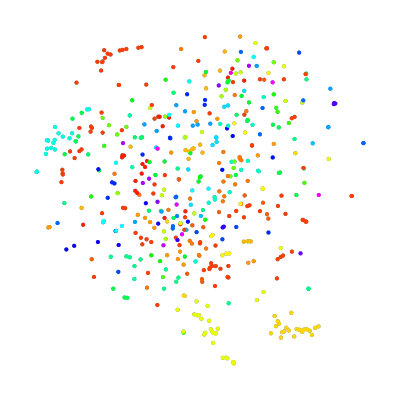

```mathematica
FeatureSpacePlot[(Tooltip[Style[#2,stockColorFunction[#1]],Column[{#1, snpSectorsAll[#1]/._Missing-> "Uncategorized"},Center]])&@@@Normal[stockReturnsPlot],LabelingFunction->None]
```

This nonfunctional manipulate calls on stockColorFunction and the stock names to color code the names.

```mathematica
Manipulate[Style[#["Name"],stockColorFunction[#]]&/@Keys[moreReturns],{stylizer,Reverse/@Normal[sectorsMapped],ControlType-> TogglerBar,Appearance-> "Row"}];
```

## Dynamic Stock Manipulator

The next step was to make my plot dynamic, because the toggler buttons did not yet work. To do this, I had to break down my code and put aside the FeatureSpacePlot.

This code uses conditionals and MemberQ to determine if a stock is a member of a particular sector. All of the stock names are white to begin with, and toggling one of the sector buttons reveals all of the corresponding stocks.

```mathematica
Prototype= Manipulate[Style[#["Name"],If[MemberQ[stylizer,stockColorFunction[#]],stockColorFunction[#],White]]&/@Keys[moreReturns],{stylizer,Reverse/@Normal[sectorsMapped],ControlType-> TogglerBar,Appearance-> "Row"}]
```

## Results!

Once I had my dynamic stock color manipulator, I put the code back into the FeatureSpacePlot to create an interactive stock sector visualizer. The user can toggle buttons to highlight the corresponding stocks.

```mathematica
Manipulate[FeatureSpacePlot[(Tooltip[Style[#2,If[MemberQ[stylizer,stockColorFunction[#]],stockColorFunction[#],White]],If[MemberQ[stylizer,stockColorFunction[#]],Column[{#1, snpSectorsAll[#1]/._Missing-> "Uncategorized"},Center]]])&@@@Normal[stockReturnsPlot],LabelingFunction->None],{stylizer,Reverse/@Normal[sectorsMapped],ControlType-> TogglerBar,Appearance-> "Row"}]
```

### Rasterized

As a small extension, I rasterized the DateListPlots to see how the machine would react to pictures instead of plots. This result would ideally be more similar to how humans would compare two stocks, as we can’t analyze individual data points in a graph.

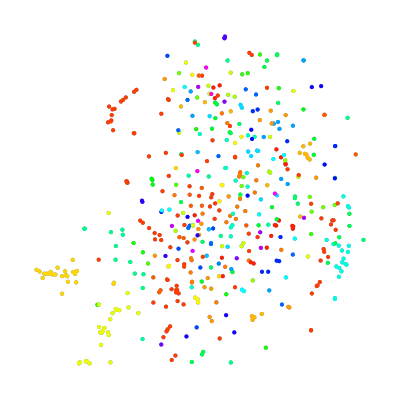

```mathematica
FeatureSpacePlot[(Tooltip[Style[#2,stockColorFunction[#1]],Column[{#1, snpSectorsAll[#1]/._Missing-> "Uncategorized"},Center]])&@@@Normal[Rasterize/@stockReturnsPlot],LabelingFunction->None]
```

## Condensing the Sectors

Although I achieved the results I wanted, the interactive plot was not very user friendly. Some industries, such as Banks and Insurance, were completely different colors, despite being in the same industry. In addition, forty three toggler buttons was too much. After remapping the industries to sectors, I created an association to assign the sectors to 12 colors. The final plot is a lot more user friendly, and it is easier to read the data.

The “Sector” property of FinancialData returns one of 50+ industries, so I manually condensed these down to the 11 commonly known sectors and one for missing sector data.

```mathematica
twelveStockSectors=<| Flatten[stockSectorsAll/@{EntityClass["Financial","Entertainment"],EntityClass["Financial","CommunicationEquipment"],EntityClass["Financial","CommunicationServices"]}]->  "Communication Services",
Flatten[stockSectorsAll/@{EntityClass["Financial","TravelAndLeisure"],EntityClass["Financial","AdvertisingAndMarketingServices"],EntityClass["Financial","PersonalServices"],EntityClass["Financial","ManufacturingApparelAndFurniture"],EntityClass["Financial","HomebuildingAndConstruction"],EntityClass["Financial","Restaurants"],EntityClass["Financial","Autos"],EntityClass["Financial","RetailApparelAndSpecialty"]}]->  "Consumer Discretionary",
Flatten[stockSectorsAll/@{EntityClass["Financial","RetailDefensive"],EntityClass["Financial","BeveragesAlcoholic"],EntityClass["Financial","ConsumerPackagedGoods"],EntityClass["Financial","TobaccoProducts"]}]->  "Consumer Staples",
 Flatten[stockSectorsAll/@{EntityClass["Financial","InsuranceSpecialty"],EntityClass["Financial","Banks"],EntityClass["Financial","BrokersAndExchanges"],EntityClass["Financial","Insurance"],EntityClass["Financial","CreditServices"],EntityClass["Financial","REITs"]}]-> "Financials",
 Flatten[stockSectorsAll/@{EntityClass["Financial","HealthCareProviders"],EntityClass["Financial","MedicalDistribution"],EntityClass["Financial","MedicalDiagnosticsAndResearch"],EntityClass["Financial","DrugManufacturers"]}]-> "Healthcare",
 Flatten[stockSectorsAll/@{EntityClass["Financial","TruckManufacturing"],EntityClass["Financial","EngineeringAndConstruction"],EntityClass["Financial","IndustrialDistribution"],EntityClass["Financial","TransportationAndLogistics"],EntityClass["Financial","AerospaceAndDefense"],EntityClass["Financial","BusinessServices"],EntityClass["Financial","Airlines"],EntityClass["Financial","ConsultingAndOutsourcing"],EntityClass["Financial","IndustrialProducts"]}]-> "Industrials",
Flatten[stockSectorsAll/@{EntityClass["Financial","ComputerHardware"],EntityClass["Financial","Semiconductors"],EntityClass["Financial","ApplicationSoftware"]}]->  "Information Technology",
 Flatten[stockSectorsAll/@{EntityClass["Financial","BuildingMaterials"],EntityClass["Financial","MetalsAndMining"],EntityClass["Financial","Chemicals"]}]-> "Materials",
 stockSectorsAll[EntityClass["Financial","RealEstateServices"]]->  "Real Estate",
stockSectorsAll[EntityClass["Financial","UtilitiesRegulated"]]->  "Utilities",
 stockSectorsAll[Missing["NotAvailable"]]->  "Unclassed"
|>
```

This creates a table of distinct, easy to see colors for the 12 sectors.

```mathematica
smallColorTable={RGBColor[0.11,0.84,0.85],RGBColor[0.7,0.34,0.8],RGBColor[0.86,0.1,0.15],RGBColor[0.08,0.7,0.15],RGBColor[0.54,0.5,0.95],RGBColor[0.38,0.34,0.35],RGBColor[0.93,0.44,0.07],RGBColor[0.56,0.32,0.],RGBColor[0.09,0.22,0.94],RGBColor[0.86,0.83,0.06],RGBColor[0.79,0.45,0.59]}
```

{RGBColor[0.11, 0.84, 0.85],RGBColor[0.7, 0.34, 0.8],RGBColor[0.86, 0.1, 0.15],RGBColor[0.08, 0.7, 0.15],RGBColor[0.54, 0.5, 0.95],RGBColor[0.38, 0.34, 0.35],RGBColor[0.93, 0.44, 0.07],RGBColor[0.56, 0.32, 0.],RGBColor[0.09, 0.22, 0.94],RGBColor[0.86, 0.83, 0.06],RGBColor[0.79, 0.45, 0.59]}

```mathematica
condensedSectorsMapped=AssociationThread[Values[twelveStockSectors]-> smallColorTable]
```

<|Communication Services→RGBColor[0.11, 0.84, 0.85],Consumer Discretionary→RGBColor[0.7, 0.34, 0.8],Consumer Staples→RGBColor[0.86, 0.1, 0.15],Financials→RGBColor[0.08, 0.7, 0.15],Healthcare→RGBColor[0.54, 0.5, 0.95],Industrials→RGBColor[0.38, 0.34, 0.35],Information Technology→RGBColor[0.93, 0.44, 0.07],Materials→RGBColor[0.56, 0.32, 0.],Real Estate→RGBColor[0.09, 0.22, 0.94],Utilities→RGBColor[0.86, 0.83, 0.06],Unclassed→RGBColor[0.79, 0.45, 0.59]|>

This maps all of the stocks to their new sector.

```mathematica
snpSectorsAll2=Association@Flatten[Function[{stockNames,sectorName},#-> sectorName &/@stockNames]@@@Normal[twelveStockSectors]];
```

updated stockColorFunction.

```mathematica
stockColorFunction2[a_]:= condensedSectorsMapped[snpSectorsAll2[a]]
```

## new and improved

I replotted the data points, but with the new color mapping. The results are a lot more user friendly, and it is easier to spot patterns.

```mathematica
alright=Manipulate[FeatureSpacePlot[(Tooltip[Style[#2,If[MemberQ[sectors,stockColorFunction2[#]],stockColorFunction2[#],White]],If[MemberQ[sectors,stockColorFunction2[#]],Column[{#1, snpSectorsAll2[#1]/._Missing-> "Uncategorized"},Center]]])&@@@Normal[stockReturnsPlot],LabelingFunction->None,PlotStyle->PointSize[Medium]],{sectors,Reverse/@Normal[condensedSectorsMapped],ControlType-> TogglerBar,Appearance-> "Row"}]
```

Here, the Financials, Information Technology, and Utilities sectors are selected. The correlation between sectors of various stocks is quite strong here. All of the yellow Utility stocks cluster in the left, while the Financial and IT sectors cluster in smaller subgroups all around the plot.

## Future Work

I focused on the visualization of stocks by sector for a fixed time frame, but there are many ways to expand the scope and give more comprehensive results. One such extension is adjusting the size of the dots to indicate market capitalization. This would show additional correlation, as one would expect larger stocks to cluster together. Another extension is to create an adjustable timeframe to see the market change over a period of time. This would be great to visualize the dynamic market, as well as to predict where the market is headed.